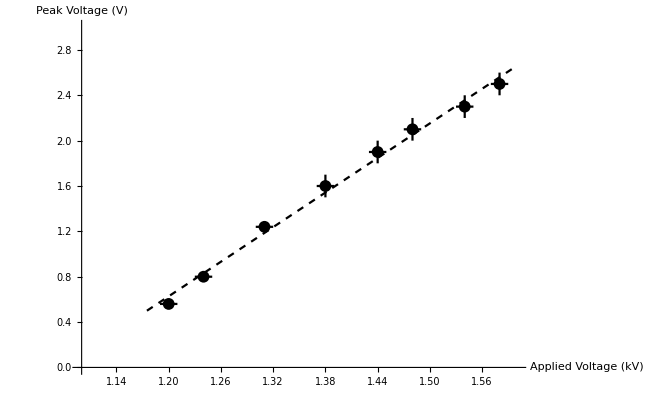

```mathematica
Needs["ErrorBarPlots`"]

data={{1.24, 0.8},{1.31, 1.24},{1.38, 1.6},{1.44, 1.9},{1.48, 2.1},{1.54, 2.3},{1.58, 2.5}, {1.2, 0.56}};
model=LinearModelFit[data,x,x];

P1=ErrorListPlot[{{{1.24, 0.8}, ErrorBar[.01,.04]},{{1.31, 1.24}, ErrorBar[.01, .04]},{{1.38, 1.6}, ErrorBar[.01, .1]},{{1.44, 1.9}, ErrorBar[.01, .1]},{{1.48, 2.1}, ErrorBar[.01, .1]},{{1.54, 2.3}, ErrorBar[.01, .1]},{{1.58, 2.5},ErrorBar[.01, .1]}, {{1.2, 0.56}, ErrorBar[.01, .04]}}, PlotRange->{{1.1, 1.6}, {0, 3}}, PlotStyle->Black];
P2=Plot[model[x], {x, 1.175, 1.6}, PlotStyle->{Black, Dashed}];
Show[P1, P2, AxesLabel->{Style["Applied Voltage (kV)", FontSize->14, FontColor->Black], Style["Peak Voltage (V)", FontSize->14, FontColor->Black]}, FrameTicksStyle->{FontSize->20}]
```

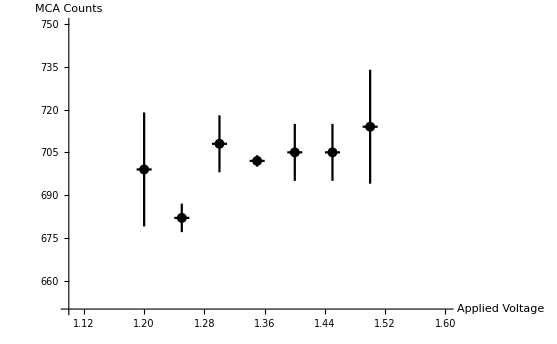

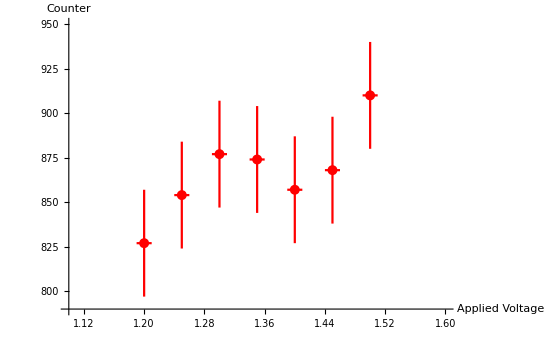

```mathematica
P1=ErrorListPlot[{{{1.2, 699}, ErrorBar[.01,20]},{{1.25, 682}, ErrorBar[.01, 5]},{{1.3, 708}, ErrorBar[.01, 10]},{{1.35, 702}, ErrorBar[.01, 2]},{{1.4, 705}, ErrorBar[.01, 10]},{{1.45, 705}, ErrorBar[.01, 10]},{{1.5, 714},ErrorBar[.01, 20]}}, PlotRange->{{1.1, 1.6}, {650, 750}}, PlotStyle->Black, AxesLabel->{Style["Applied Voltage", FontSize->14, FontColor->Black], Style["MCA Counts", FontSize->14, FontColor->Black]}]
P2=ErrorListPlot[{{{1.2, 827}, ErrorBar[.01,30]},{{1.25, 854}, ErrorBar[.01, 30]},{{1.3, 877}, ErrorBar[.01, 30]},{{1.35, 874}, ErrorBar[.01, 30]},{{1.4, 857}, ErrorBar[.01, 30]},{{1.45, 868}, ErrorBar[.01, 30]},{{1.5, 910},ErrorBar[.01, 30]}}, PlotRange->{{1.1, 1.6}, {790, 950}}, PlotStyle->Red, AxesLabel->{Style["Applied Voltage", FontSize->14, FontColor->Black], Style["Counter", FontSize->14, FontColor->Black]}]
Show[P1, P2, PlotRange->{{1.1, 1.6},{650, 950}}];
```